```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lyliana/Documentos/Wolfram Mathematica/FIsExp

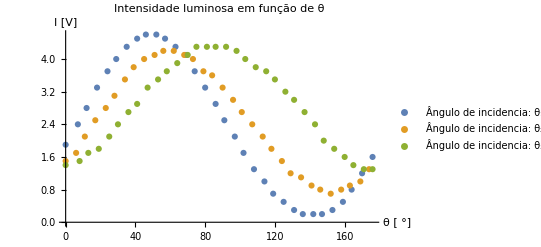

```mathematica
dados = Import["DadosA3.dat"];
colunas = Transpose[dados];
g1 = Transpose[{colunas[[1]],colunas[[2]]}];
g2 = Transpose[{colunas[[3]],colunas[[4]]}];
g3 = Transpose[{colunas[[5]],colunas[[6]]}];
grafico=ListPlot[{g1,g2,g3}, PlotLabel->"Intensidade luminosa em função de θ", PlotLegends->{"Ângulo de incidencia: θ_1 = (47±1 grau)","Ângulo de incidencia: θ_2 = (67±1 grau)","Ângulo de incidencia: θ_3 =  (76±1 grau)"}, AxesLabel->{"θ [ °]","I [V]"}]
```

Aqui temos o ajuste da intensidade em função dos parâmetros I_0, η, ξ:

```mathematica
intensidade[θ_]:= I0*( 1 - (η*Sin[2*θ Degree]) + (ξ*Cos[2*θ Degree]));
```

Definindo  ψ e Δ  em função η e ξ.

```mathematica
ψ[ξ_, α_]:= ArcTan[(√(1 + ξ))/(√(1 - ξ))*Abs[Tan[α Degree] Degree]]
incψ[ξ_, α_, incξ_, incα_]:= √(( incξ* Derivative[ψ[ξ, α],ξ ])^2 + (incα*Derivative[ψ[ξ, α], α])^2) //Degree

Δ[ η_, ξ_, α_]:= ArcCos[η/(√(1 - ξ^2))* Sign[α] Degree] 
incΔ[ η_, ξ_, α_, incη_,incξ_, incα_]:= √(( incη* D[Δ[ η, ξ, α],η ])^2  +( incξ* D[Δ[ η,ξ, α],ξ ])^2 + (incα*D[Δ[ η,ξ, α], α])^2) //Degree
```

### Ângulo de incidencia: θ_1 = (47±1 grau)

Ângulo de incidencia: θ_1 = (47±1 grau)

{I0→2.31489,η→-0.941993,ξ→-0.158843}

{0.0123264,0.00904191,0.00757753}

0.999377

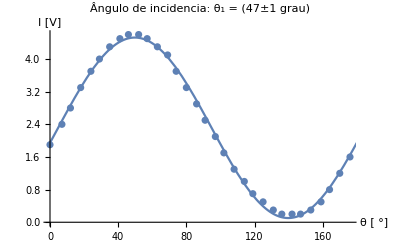

29

```mathematica
Print[ "Ângulo de incidencia: θ_1 = (47±1 grau)"]
ajusteg1 = NonlinearModelFit[g1,intensidade[θ], {{I0}, {η},{ξ}},θ];
ajusteg1["BestFitParameters"]
ajusteg1["ParameterErrors"]
ajusteg1["AdjustedRSquared"]
a =Show[{ListPlot[g1],Plot[intensidade[θ]/.ajusteg1["BestFitParameters"],{θ,0 ,180}]},PlotLabel-> "Ângulo de incidencia: θ_1 = (47±1 grau)", AxesLabel->{"θ [ °]","I [V]"}]
Length[g1] - 3
```

```mathematica
Subscript[ψ, 1] = ψ[-0.1588,45];
Subscript[Δ, 1] = Δ[-0.9420,-0.1588, 45];
Print["ψ_1 =  ",Subscript[ψ, 1]," [V]"]
Print["Δ_1 = ",Subscript[Δ, 1], " [V]"]
```

ψ_1 =  0.0148693 [V]

Δ_1 = 1.58745 [V]

### Ângulo de incidencia: θ_2 = (67±1 grau)

Ângulo de incidencia: θ_2 = (67±1 grau)

{I0→2.45,η→-0.590289,ξ→-0.373345}

{0.0117894,0.00737424,0.00703837}

0.999405

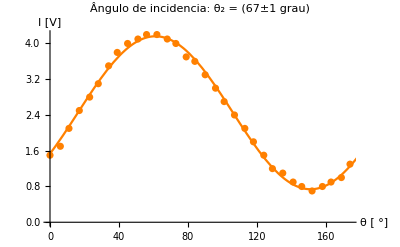

29

```mathematica
Print[ "Ângulo de incidencia: θ_2 = (67±1 grau)"]
ajusteg2erro = NonlinearModelFit[g2, intensidade[θ], {{I0}, {η},{ξ}},θ];
ajusteg2erro["BestFitParameters"]
ajusteg2erro["ParameterErrors"]
ajusteg2erro["AdjustedRSquared"]
b = Show[{  ListPlot[g2, PlotStyle->Orange],Plot[intensidade[x]/.ajusteg2erro["BestFitParameters"],{x,0 ,180},  PlotStyle->Orange] }, PlotLabel-> "Ângulo de incidencia: θ_2 = (67±1 grau)", AxesLabel->{"θ [ °]","I [V]"}]
Length[g2] - 3
```

```mathematica
Subscript[ψ, 2] = ψ[-0.3733, 45];
Subscript[Δ, 2] = Δ[ -0.5903,-0.3733, 45];
Print["ψ_2 =  ",Subscript[ψ, 2], " [V]"]
Print["Δ_2 =  ",Subscript[Δ, 2], "  [V]"]
```

ψ_2 =  0.0117897 [V]

Δ_2 =  1.5819  [V]

### Ângulo de incidencia: θ_3 = (76±1 grau)

Ângulo de incidencia: θ_3 =  (76±1 grau)

{I0→2.87869,η→-0.0717181,ξ→-0.510092}

{0.0131866,0.00648656,0.00688561}

0.999407

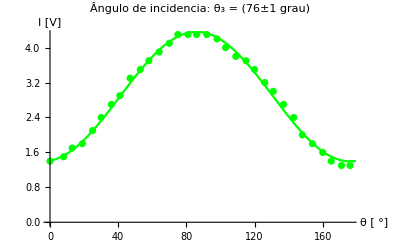

29

```mathematica
Print[ "Ângulo de incidencia: θ_3 =  (76±1 grau)"]
ajusteg3erro = NonlinearModelFit[g3,intensidade[θ], {{I0}, {η},{ξ}},θ];
ajusteg3erro["BestFitParameters"]
ajusteg3erro["ParameterErrors"]
ajusteg3erro["AdjustedRSquared"]
c = Show[{ListPlot[g3, PlotStyle->Green],Plot[intensidade[x]/.ajusteg3erro["BestFitParameters"],{x,0 ,180},  PlotStyle->Green] }, PlotLabel-> "Ângulo de incidencia: θ_3 =  (76±1 grau)", AxesLabel->{"θ [ °]","I [V]"}]
Length[g3] - 3
```

```mathematica
Subscript[ψ, 3] = ψ[-0.5101, 45] ;
Subscript[Δ, 3] = Δ[ -0.0717, -0.5101, 45];
Print["ψ_3 =  ",Subscript[ψ, 3], " [V]"]
Print["Δ_3 =  ",Subscript[Δ, 3], " [V]"]
```

ψ_3 =  0.00994063 [V]

Δ_3 =  1.57225 [V]

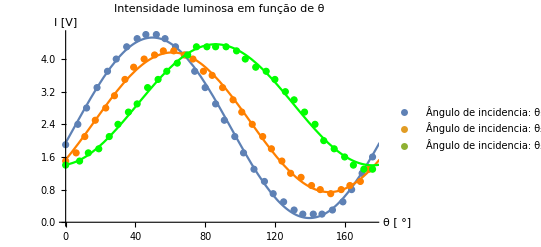

```mathematica
Show[{grafico, a , b, c}]
```

```mathematica
N
```